### msBBGgetHistory example.

Be sure to set the correct path to your executable.

```mathematica
Options[msBBGgetHistoryMakeLinkObject]={"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGgetHistory.exe"}]]};
msBBGgetHistoryMakeLinkObject[OptionsPattern[]]:=Install[OptionValue["path to executable"]];msBBGgetHistoryMakeLinkObject::usage = "msBBGgetHistoryMakeLinkObject[]: When run, launches the WSTP application that moves historical securities data from Bloomberg to Mathematica. msBBGgetHistory[] will launch and kill this automatically, but you can do it manually with this function, assign the result to a variable, and pass the link to msBBGgetHistory[] with the \"LinkObject]\"→ option if you plan on calling it many times in succession.  This saves the overhead of relaunching the link for every call. When finished, can call Uninstall[(this link)] and the program will be quit. Can set \"path to executable\" variable if the default is for some reason not what you want.";

Options[msBBGgetHistory]={"adjust"->"CALENDAR","type"->"value","name"->"df","output"->"nf3"(* vs. "nf2" or "ts"*),"keep link active"->False,"noisy"->False,"use DPDF"->False,"LinkObject"->Null,"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGgetHistory.exe"}]]};
msBBGgetHistory[ticker_String,field_String,start_,end_,freq_String,OptionsPattern[]]:= Module[{raw,name1,output,link, date,endS},
name1=If[OptionValue["name"]=="df",ticker<>": "<>field,OptionValue["name"]];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
date=Switch[ToUpperCase[freq] ,"DAY","DAILY","WEEK","WEEKLY","MONTH","MONTHLY","QUARTER","QUARTERLY","YEAR","YEARLY","ANNUAL","YEARLY",_,ToUpperCase[freq]];
 endS=Switch[Head[end],List,DateString[end,{"Year","Month","Day"}],DateObject,DateString[end,{"Year","Month","Day"}],String,end];raw =msBBGgetHistory[ticker, field,DateString[start,{"Year","Month","Day"}],If[endS=="",endS,DateString[end,{"Year","Month","Day"}]],date,ToUpperCase[OptionValue["adjust"]],If[OptionValue["use DPDF"],1,0],If[OptionValue["noisy"],1,0]]; 
output=If[OptionValue["noisy"],raw,ToExpression[raw]];(* use ToExpression to convert C++ string output into list *)
(*If[OptionValue["noisy"],Print["raw: ",raw]];*)
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
Which[
!OptionValue["noisy"](*&&StringLength[output]>0*),output=Map[{Take[DateList[#[[1]]],3],#[[2]]}&,output];
output=Switch[OptionValue["type"],"value",TimeSeries[output],"pctchanges",EventSeries[output],"delta",EventSeries[output]];
output=Switch[OptionValue["output"],
"nf2",Association["name"->name1,"type"->OptionValue["type"],"data"->output],
"nf3",TemporalData[output,MetaInformation->{"name"->name1,"type"->OptionValue["type"]}],
"ts",output],
!OptionValue["noisy"]&& StringLength[output]==0,output="Data not found. For more information, run with \"noisy\"→True",
OptionValue["noisy"],output
]
];
msBBGgetHistory::usage = 
"msBBGgetHistory[ticker_,field_,start_,end_,freq_,OptionsPattern[]] retrieves data from Bloomberg for a given ticker and field within the specified period.
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
field: e.g., \"Px_Last\"
start: start date
end: end date, or \"\" for current day
freq: is the data frequency. Choices: \"day\", \"week\", \"month\", \"quarter\", or \"year\"\n

Optionally, you can pass  adjust→ for the period adjustment (default is \"CALENDAR\"). Choices, \"ACTUAL\", \"CALENDAR\"
type→ is one of \"delta\", \"pctchanges\", or (by default) \"value\". 
name→\"whatever\" sets the name.
\"output\"→\"nf2\", \"nf3\" (the new default) or \"ts\". nf2 is an association with Keys \"data\", \"name\" and \"type\". nf3 is a TemporalData object with the same information in MetaInformation. \"ts\" leaves out the MetaInformation.
\"noisy\"→(True or False), toggles debugging info
\"use DPDF\"→(True or False), toggles whether or not the DPDF settings in the Bloomberg terminal are respected. This would typically be used to shut off dividend adjustment, if it has been turned on.
\"LinkObject\" can be passed a link object created by msBBGgetHistoryMakeLinkObject[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.

By default, pctchanges and delta-type data are stored as EventSeries[], while value-type data is stored as TimesSeries[]." ;
```

```mathematica
msBBGgetHistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->False]
```

TemporalData[…]

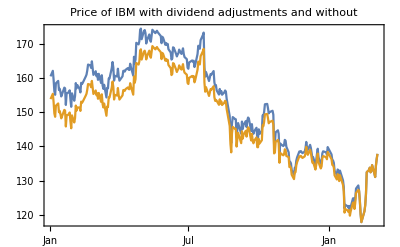

```mathematica
histLink=msBBGgetHistoryMakeLinkObject;
x1=msBBGgetHistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->False,LinkObject->histLink];
x2=msBBGgetHistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->True,LinkObject->histLink];
DateListPlot[{x1,x2},PlotLabel->"Price of IBM with dividend adjustments and without"]
```